## Illustration of a wavy circle

```mathematica
points=N@CirclePoints[1,4*16];
pA=points⟦1;;;;4⟧;
pB=points⟦2;;;;4⟧*1.2;
pC=points⟦3;;;;4⟧;
pD=points⟦4;;;;4⟧*0.8;
```

```mathematica
Graphics[{
BSplineCurve[Flatten[{pA,pB,pC,pD}ᵀ,1],SplineClosed->True],
PointSize[Medium],
Red,Point[pA],
Green,Point[pB],
Blue,Point[pC],
Black,Point[pD],
Dashed,Circle[]
}]
```

-Graphics-

### With an arrowhead

```mathematica
DynamicModule[{x},
Grid[{
{Slider[Dynamic[x],{0,1}]},
{Dynamic[
Graphics[{
Arrowheads[{{0.1,x}}],
Arrow[BSplineCurve[Append[Flatten[{pA,pB,pC,pD}ᵀ,1],First@pA]]]
}]
]}
}]
]
```

## Difference between BSpline and Bezier curves

```mathematica
AA=ReIm@RandomComplex[];
BB=ReIm@RandomComplex[];
CC=ReIm@RandomComplex[];
DD=ReIm@RandomComplex[];
EE=ReIm@RandomComplex[];
```

```mathematica
Graphics[{
Red,Point[{AA,BB,CC,DD,EE}],
Thin,Line[{AA,BB,CC,DD,EE}],
Black,Thick,
BSplineCurve[{AA,BB,CC,DD,EE}],
Dashed,Blue,
BezierCurve[{AA,BB,CC,DD,EE},SplineDegree->4]
}]
```

-Graphics-

## Implementation

```mathematica
ClearAll[Outer1];
Outer1[func_,a_,B_List]:=Outer[func,{a},B,1]⟦1⟧;
```

```mathematica
Outer1[Times,{x,y},{1,2,3,4}]
```

{{x,y},{2 x,2 y},{3 x,3 y},{4 x,4 y}}

Changing signs of “width” and “ratio” parameters below will affect the shape of curves, whereas only the absolute value of “pitchRef” is significant.

### Wavy

```mathematica
ClearAll[WavyLine];
WavyLine[{p1_List,p2_List},pitchRef_,width_]:=Module[
{vec=p2-p1,num,pts},
num=Abs@Round[2 Norm[vec]/pitchRef];
pts=Outer1[Plus,p1,Outer1[Times,vec,Subdivide[If[num==0,1,2num]]]];
If[num>0,pts⟦2;;;;4⟧=Outer1[Plus,AngleVector[ArcTan@@vec+π/2]width,pts⟦2;;;;4⟧]];
If[num>1,pts⟦4;;;;4⟧=Outer1[Plus,-AngleVector[ArcTan@@vec+π/2]width,pts⟦4;;;;4⟧]];
BSplineCurve[pts]
]
```

```mathematica
rs=WavyLine[{{0,0},{1,0}},1,0.1];
Graphics[{
Red,Point@@rs,
Thin,Line@@rs,
Black,Thick,rs
}]
```

-Graphics-

```mathematica
ClearAll[WavyCircle];
WavyCircle[center_List,radius_,{θ1_,θ2_},pitchRef_,width_]:=Module[
{δ=θ2-θ1,num,θs,pts},
num=Abs@Round[2 δ radius/pitchRef];
θs=θ1+Subdivide[If[num==0,1,2num]]*δ;
pts=Outer1[Plus,center,(AngleVector/@θs)radius];
If[num>0,pts⟦2;;;;4⟧+=(AngleVector/@(θs⟦2;;;;4⟧+UnitStep[δ]π))width];
If[num>1,pts⟦4;;;;4⟧+=(AngleVector/@(θs⟦4;;;;4⟧+UnitStep[-δ]π))width];
BSplineCurve[pts]
]
```

```mathematica
rs=WavyCircle[{0,0},1/π,{0,π},0.1,0.1];
Graphics[{
{PointSize->Large,Point[{{0,0}}]},
Red,Point@@rs,
Thin,Line@@rs,
Black,Thick,rs
}]
```

-Graphics-

### Coiled

#### Straight line

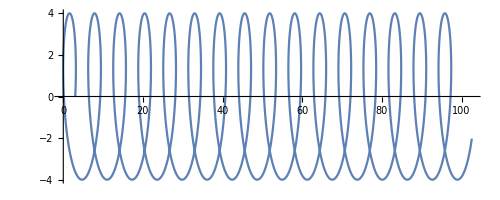

```mathematica
ParametricPlot[{x+3Cos[x],4Sin[x]},{x,0,100}]
```

p/2 n+2rp=l=||vec||
n=(2l)/p-4r
p=(2l)/(n+4r)

```mathematica
ClearAll[CoiledLine];
CoiledLine[{p1_List,p2_List},pitchRef_,width_,ratio_]:=Module[
{vec=p2-p1,num,pitch,pts},
num=Max[Round[2 Norm[vec]/Abs@pitchRef-4ratio],0];If[EvenQ[num],num++];
pitch=2Norm[vec]/(num+4ratio);
pts=Outer1[Plus,p1+(1/2-(num pitch)/(4Norm[vec]))vec,Outer1[Times,(num pitch)/(2Norm[vec])vec,Subdivide[2num]]];
pts⟦1;;;;4⟧=Outer1[Plus,-AngleVector[ArcTan@@vec]ratio pitch,pts⟦1;;;;4⟧];
pts⟦2;;;;4⟧=Outer1[Plus,AngleVector[ArcTan@@vec+π/2]width,pts⟦2;;;;4⟧];
pts⟦3;;;;4⟧=Outer1[Plus,AngleVector[ArcTan@@vec] ratio pitch,pts⟦3;;;;4⟧];
If[num>1,pts⟦4;;;;4⟧=Outer1[Plus,AngleVector[ArcTan@@vec-π/2]width,pts⟦4;;;;4⟧]];
BSplineCurve[pts]
]
```

```mathematica
rs=CoiledLine[{{0,0},{1,0}},0.1,0.1,3/4];
Graphics[{
{PointSize->Large,Point[{{0,0},{1,0}}]},
Red,Point@@rs,
Thin,Line@@rs,
Black,Thick,rs
}]
```

-Graphics-

#### Arc

α/2 n+2r α=δ
n=(2δ)/α-4r
α=(2δ)/(n+4r)

```mathematica
ClearAll[CoiledCircle];
CoiledCircle[center_List,radius_,{θ1_,θ2_},pitchRef_,width_,ratio_]:=Module[
{δ=θ2-θ1,num,α,θs,pts},
num=Max[Round[Abs[2 δ radius/pitchRef]-4ratio],0];If[EvenQ[num],num++];
α=Abs[2δ]/(num+4ratio);
θs=θ1+1/2 δ-(num α)/4+Subdivide[num/2,2num]α;
θs⟦1;;;;4⟧-=ratio α;
θs⟦3;;;;4⟧+=ratio α;
pts=Outer1[Plus,center,(AngleVector/@θs)radius];
pts⟦2;;;;4⟧+=(AngleVector/@(θs⟦2;;;;4⟧+UnitStep[δ]π))width;
If[num>1,pts⟦4;;;;4⟧+=(AngleVector/@(θs⟦4;;;;4⟧+UnitStep[-δ]π))width];
BSplineCurve[pts]
]
```

```mathematica
rs=CoiledCircle[{0,0},1/π,{π,0},0.1,0.1,3/4];
Graphics[{
{PointSize->Large,Point[{{0,0},{1/π,0},{-1/π,0}}]},
Red,Point@@rs,
Thin,Line@@rs,
Black,Thick,rs
}]
```

-Graphics-